Figure for amperesLawBetweenTwoCurrents.eps.  Circles surrounding two currents, with respective phicap vectors around those sources.

```mathematica
<<peeters` ;
peeters`setGitDir[ "../project/figures/GAelectrodynamics" ]
```

/Users/pjoot/project/figures/GAelectrodynamics

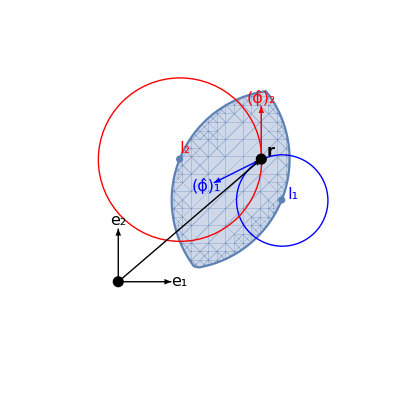

```mathematica
ClearAll[o,e1,e1,stuff, fs, bold, rot90, plot1]
o = {0,0};
{e1,e2} = IdentityMatrix[2];

rot90 = RotationMatrix[Pi/2];
bold = Style[ #, Bold] &;
fs = Style[ #, FontSize->16]&;

stuff[center_, boundingPt_, idx_, color_, one_] := Module[{radius,r,rcap, phicap},
r = boundingPt - center;
rcap = r // Normalize;
phicap = rot90.rcap;
radius = r// Norm;
{
color,
Circle[center,radius],
Text[Subscript["I", idx]//fs,center + 0.15 Normalize[center]],
Arrow[ {boundingPt, boundingPt + phicap one}],
Text[Subscript[OverHat["ϕ"], idx]//fs,boundingPt + phicap one 1.15]
}];

plot1 = Module[{p1,p2,(*p3,*)r, range, one, rr, range2},
p1 = {2,1};
p2 = {1,2}0.75;
rr = Norm[p1-p2];
(*p3 = {2,2};*)
r = {1.75,1.5};
range = {-0.5,2.75};
range2 = 10;
one = 0.65;
Show[{

RegionPlot[
(x-p1[[1]])^2+(y-p1[[2]])^2<rr^2 &&
(x-p2[[1]])^2+(y-p2[[2]])^2<rr^2
,{x,-1,3},{y,-1,3}, Ticks -> None, Frame -> None],
ListPlot[ {p1, p2}, AspectRatio -> 1, PlotRange->{range,range}, Ticks -> None],
Graphics[
Flatten[
{
 stuff[p1,r,1,Blue, one],
 stuff[p2,r,2,Red, one],
{
Black,
Arrow[{o,r}],
Arrow[{o,e1 one}],
Arrow[{o,e2 one}],
Text["r" // bold // fs, r + 0.15 Normalize[r]],
Text[Subscript["e", 1]//fs,e1 one 1.15],
Text[Subscript["e", 2]//fs,e2 one 1.15],

PointSize->0.02,
Point[{o,r}]
}
},
1]
]
}]
]
```

```mathematica
peeters`exportForLatex["amperesLawBetweenTwoCurrents", plot1]
```

{amperesLawBetweenTwoCurrents.eps,amperesLawBetweenTwoCurrentspn.png}